```mathematica
numberTriangulations=Import[NotebookDirectory[]<>"data/data-number-triangulations.csv"][[5;;]];
```

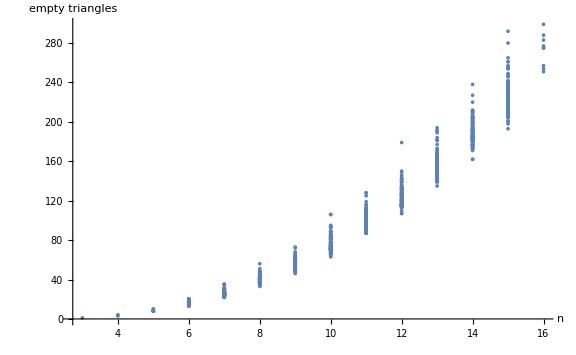

```mathematica
ListPlot[numberTriangulations[[All,{1,3}]],ImageSize->Large,LabelStyle->Medium,AxesLabel->{"n","empty triangles"}]
```

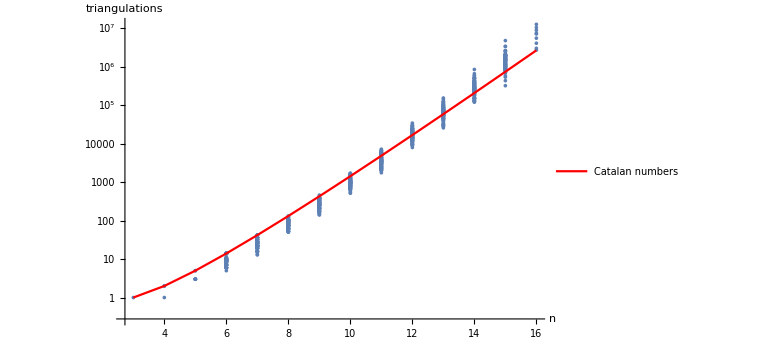

```mathematica
Show[
ListLogPlot[numberTriangulations[[All,{1,4}]],ImageSize->Large,LabelStyle->Medium,AxesLabel->{"n","triangulations"}],
ListLinePlot[Table[{n,Log@CatalanNumber[n-2]},{n,3,16}],PlotLegends->{"Catalan numbers"},PlotStyle->Red]
]
```

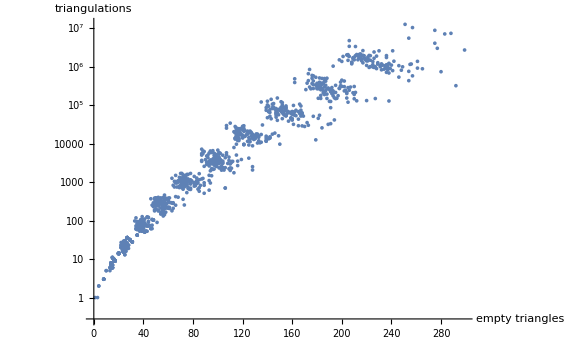

```mathematica
ListLogPlot[numberTriangulations[[All,{3,4}]],ImageSize->Large,LabelStyle->Medium,AxesLabel->{"empty triangles","triangulations"}]
```

```mathematica
getPointCloud[path_]:=With[{initialTriangulation=Import[path,"Table"]//Rest},
Graphics[Point[Partition[Flatten[initialTriangulation],2]]]
];
```

```mathematica
getSpectrum[path_]:=With[{spectrum=Flatten[Import[path,"Table"]]},
Histogram[spectrum,(*Max[{Quotient[Length[spectrum],10],20}]*)50,LabelStyle->Medium,ChartStyle->Blue]
];
```

```mathematica
globalDataConvex=Table[Import[NotebookDirectory[]<>"instances/convex-"<>ToString[i]<>"/gap","Table"],{i,5,15}];
sizesConvex=globalData[[All,2]]//Flatten
gapsConvex=globalData[[All,4]]//Flatten
```

{5,14,42,132,429,1430,4862,16796,58786,208012,742900}

{0.690983,0.333332,0.192011,0.123317,0.0852506,0.0621458,0.0471519,0.0369086,0.0296226,0.0242653,0.0202193}

```mathematica
globalDataUniform=Table[Import[NotebookDirectory[]<>"instances/uniform-"<>ToString[i]<>"/gap","Table"],{i,5,15}];
sizesUniform=globalDataUniform[[All,2]]//Flatten
gapsUniform=globalDataUniform[[All,4]]//Flatten
```

{3,6,26,63,191,282,3643,17656,90443,430602,1081390}

{1,0.422649,0.170734,0.0952003,0.0580273,0.0770497,0.0332738,0.0230281,0.0176849,0.0149412,0.0126386}

```mathematica
Show[ListLogLogPlot[{
{Table[i,{i,5,15}],gapsConvex}//Transpose,
{Table[i,{i,5,15}],gapsUniform}//Transpose
},ImageSize->Large,PlotLabels->{"convex","uniform"},AxesLabel->{"n","spectral gap"}],
LogLogPlot[50/x^3,{x,5,15},PlotStyle->Red,PlotLabels->"C/n^3"]
]
```

-Graphics-

```mathematica
ListLogLogPlot[{
{Table[i,{i,5,15}],gapsConvex/2}//Transpose,
{Table[i,{i,5,15}],Sqrt[2gapsConvex]}//Transpose
},ImageSize->Large,PlotLabels->{"upper bound","lower bound"},AxesLabel->{"n","connectivity"},PlotLabel->"convex connectivity"]
```

-Graphics-

```mathematica
ListLogLogPlot[{
{Table[i,{i,5,15}],gapsUniform/2}//Transpose,
{Table[i,{i,5,15}],Sqrt[2gapsUniform]}//Transpose
},ImageSize->Large,PlotLabels->{"upper bound","lower bound"},AxesLabel->{"n","connectivity"},PlotLabel->"uniform connectivity"]
```

-Graphics-

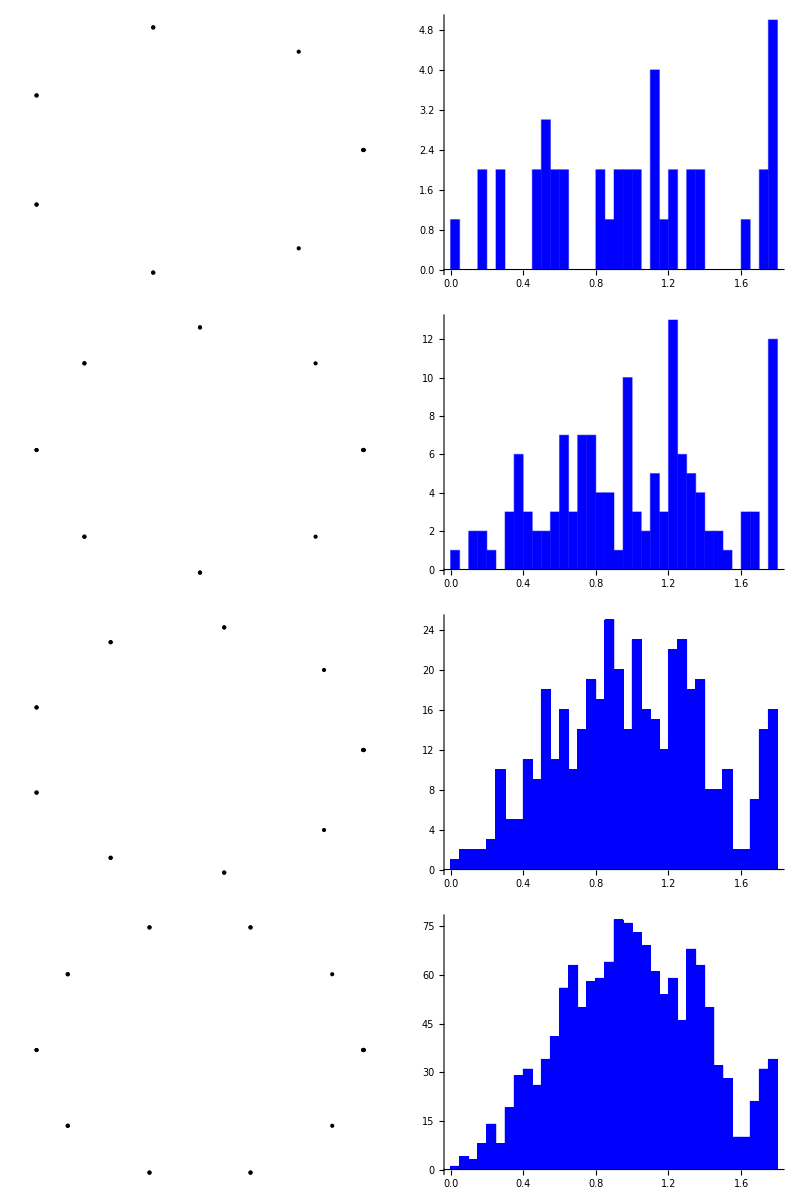

```mathematica
prefix=NotebookDirectory[]<>"instances/convex-";
Grid[Table[{getPointCloud[prefix<>ToString[i]<>"/initial-triangulation"],getSpectrum[prefix<>ToString[i]<>"/spectrum"]},{i,7,10}],Frame->All]
```

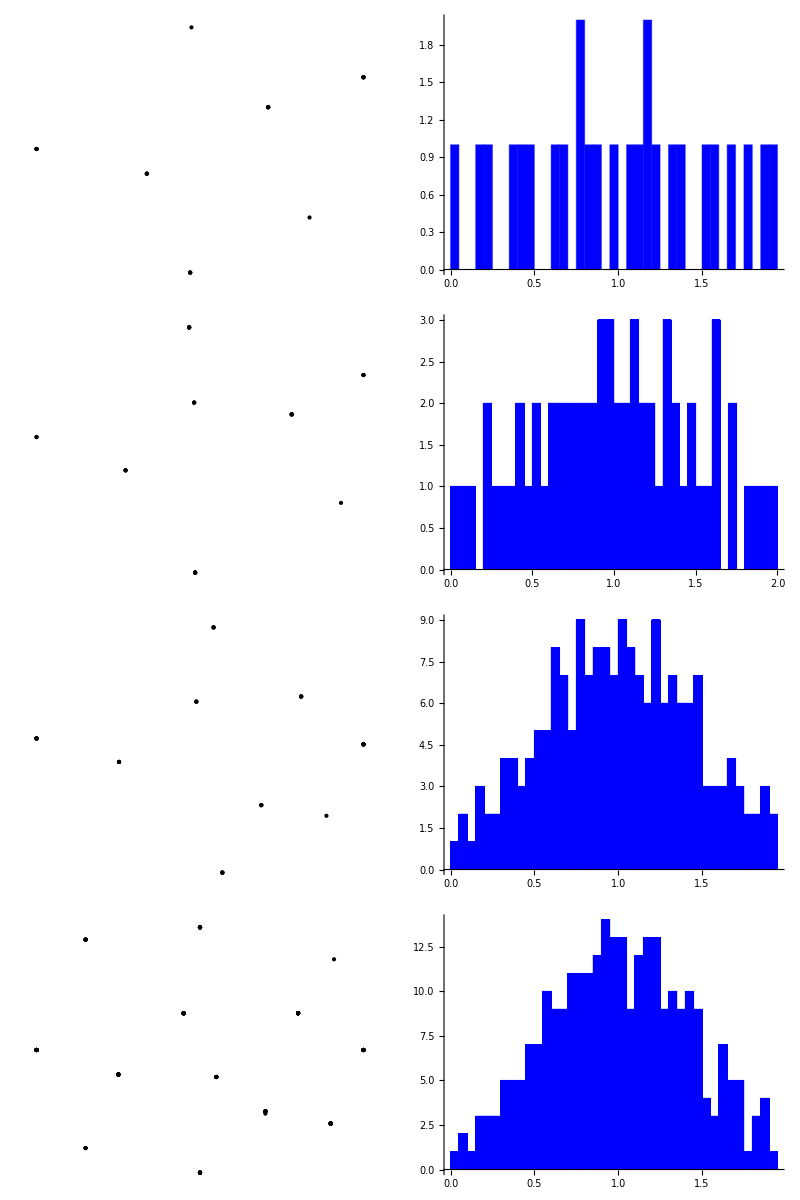

```mathematica
prefix=NotebookDirectory[]<>"instances/uniform-";
Grid[Table[{getPointCloud[prefix<>ToString[i]<>"/initial-triangulation"],getSpectrum[prefix<>ToString[i]<>"/spectrum"]},{i,7,10}],Frame->All]
```